```mathematica
Save["渦電流とドロネー図att48_関数変数データ","Global`*"]
```

```mathematica
Clear["Global`*"]
```

```mathematica
Get["渦電流とドロネー図att48_関数変数データ"];
```

### 関数

```mathematica
LoopMatrix[g_]:=(
FundLoop=FindFundamentalCycles[UndirectedGraph[g]];
RuleFundLoop=Table[EdgeRules[FundLoop[[i]]],{i,Length[FundLoop]}];
RuleRevFundLoop=Table[
EdgeRules[ReverseGraph[Graph[RuleFundLoop[[i]]]]],
{i,Length[FundLoop]}
];
Ruleg=EdgeRules[g];
Table[
Table[
If[MemberQ[RuleFundLoop[[j]],Ruleg[[i]]],1,0]+If[MemberQ[RuleRevFundLoop[[j]],Ruleg[[i]]],-1,0],
{i,EdgeCount[g]}
],
{j,Length[FundLoop]}]
)
```

```mathematica
VertexSortFromLoopEdgeList[LoopEdgeList_]:=(
UndirectedLoop=FindCycle[UndirectedGraph[LoopEdgeList]][[1]];
MinVertexNum=Min[VertexList[UndirectedLoop]];
VertexLoop={MinVertexNum};
For[j=1,Length[VertexLoop]≠ Length[UndirectedLoop],j++,
VertexLoop=Append[VertexLoop,UndirectedLoop[[FirstPosition[UndirectedLoop,VertexLoop[[j]]<->_][[1]],2]]]
];
VertexLoop=Append[VertexLoop,MinVertexNum]
)(* Vertex Sort From Loop Edge List ルールエッジで表現された巡回路から、頂点で表現された巡回路に直す *)
```

```mathematica
DelEle[list_,element_]:=list/.element->Nothing(* Delete Element *)
```

```mathematica
DelEleList[list_,elementlist_]:=list/.Table[i-> Nothing ,{i,elementlist}](* Delete Element *)
```

```mathematica
DelEdgeVertexList[edgelist_,vertexlist_]:=(
devl={};(* Variable of DelEdgeVertexList *)
Do[devl=Union[Position[edgelist,i].{{1},{0}},devl],{i,vertexlist}];
Delete[edgelist,devl]
)(* Delete Edge list from Vertex List 頂点リストから枝リストを削除（頂点リストにある頂点で構成される枝はすべて枝リストから削除）頂点リストに重複があってもUnionがあるのでOK *)
```

```mathematica
EdgeNum[Edge_]:=(
FirstPosition[EdgeRules[Gin],Edge,
FirstPosition[
EdgeRules[Gin],
EdgeRules[
ReverseGraph[{Edge}]
][[1]]
]
][[1]]
) (* Edge Number *)
```

```mathematica
EdgeNumList[Edge_]:=Table[EdgeNum[Edge[[i]]],{i,Length[Edge]}] (* Edge Number List *)
```

```mathematica
EdgeD[Edge_]:=PD[[EdgeNum[Edge]]](* Edge Distance *)
```

```mathematica
EdgeDList[Edge_]:=PD[[EdgeNumList[Edge]]](* Edge Distance *)
```

```mathematica
ListPosRef[list1_,list2_,element_]:=list1[[FirstPosition[list2,element][[1]]]](* list2でのelementの位置に来る、list1の要素を求める(list1にlist2の位置を反映 List Position Reflection) *)
```

```mathematica
EdgeReconst[Edge1_,Side1_,Edge2_,Side2_]:=VertexList[{Edge1}][[Side1]]->VertexList[{Edge2}][[Side2]](* Edge Reconstraction ２つの枝のそれぞれ片方の頂点を使って枝を再構成する *)
```

```mathematica
RestVertex[PartLoop_]:=Delete[VertexList[Gin],Table[{VertexList[PartLoop][[i]]},{i,Length[VertexList[PartLoop]]}]]
```

```mathematica
TriTourDiff[Edge_,Vertex_]:=(
EdgeD[VertexList[{Edge}][[1]]->Vertex]+EdgeD[VertexList[{Edge}][[2]]->Vertex]-EdgeD[Edge]
)(* Triangle Tour Difference *)
```

```mathematica
TriTourDiffList[PartLoop_,Vertex_]:=Table[TriTourDiff[PartLoop[[i]],Vertex],{i,Length[PartLoop]}]
```

```mathematica
MinTriTourDiffPosition[PartLoop_,Vertex_]:=(
FirstPosition[TriTourDiffList[PartLoop,Vertex],Min[TriTourDiffList[PartLoop,Vertex]]][[1]]
)
```

```mathematica
MinEdgeReconstPair[EdgePair_]:=(
ReconstEdgeD1=EdgeD[EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],1]]+EdgeD[EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],2]];
ReconstEdgeD2=EdgeD[EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],2]]+EdgeD[EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],1]];
If[
ReconstEdgeD1<ReconstEdgeD2,
{ReconstEdgeD1,{EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],1],EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],2]}},
{ReconstEdgeD2,{EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],2],EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],1]}}
]
)(* Minimum Edge Reconstraction Pair 枝ペアを再構成し、枝のコストが小さいほうのコストと枝ペアを出力 *)
```

```mathematica
SquareTourDiff[Edge1_,Edge2_]:=(
MinEdgeReconstPair[{Edge1,Edge2}][[1]]-EdgeD[Edge1]-EdgeD[Edge2]
)(* Square Tour Difference *)
```

```mathematica
SquareTourDiffList[PartLoop1_,PartLoop2_]:=Table[SquareTourDiff[i,j],{i,PartLoop1},{j,PartLoop2}]
```

```mathematica
MinSquareTourDiffEdgePair[PartLoop1_,PartLoop2_]:=(
PairNum=FirstPosition[SquareTourDiffList[PartLoop1,PartLoop2],Min[SquareTourDiffList[PartLoop1,PartLoop2]]];
{PartLoop1[[PairNum[[1]]]],PartLoop2[[PairNum[[2]]]]}
)(* 最小のスクエアツアとなるPartLoopの枝ペア *)
```

```mathematica
JoinPartLoop[PartLoop1_,PartLoop2_]:=Join[DelEleList[Join[PartLoop1,PartLoop2],MinSquareTourDiffEdgePair[PartLoop1,PartLoop2]],MinEdgeReconstPair[MinSquareTourDiffEdgePair[PartLoop1,PartLoop2]][[2]]]
```

```mathematica
RestVertexMinCost[PartLoop_]:=Table[Min[TriTourDiffList[PartLoop,i]],{i,RestVertex[PartLoop]}](* 残りの頂点のそれぞれの追加コストが最小になる位置での追加コストのリスト *)
```

```mathematica
MinRestVertex[PartLoop_]:=RestVertex[PartLoop][[
FirstPosition[RestVertexMinCost[PartLoop],Min[RestVertexMinCost[PartLoop]]][[1]]
]](* 残りの頂点の中でも最小の追加コストとなる頂点 *)
```

```mathematica
LoopDelEdge[PartLoop_]:=PartLoop[[MinTriTourDiffPosition[PartLoop,MinRestVertex[PartLoop]]]](* 頂点を追加するときに削除すべき枝 *)
```

```mathematica
InsertVertexLoop[PartLoop_]:=EdgeRules[EdgeAdd[EdgeDelete[PartLoop,LoopDelEdge[PartLoop]],{VertexList[{LoopDelEdge[PartLoop]}][[1]]-> MinRestVertex[PartLoop],MinRestVertex[PartLoop]-> VertexList[{LoopDelEdge[PartLoop]}][[2]]}]](* １つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
ContinuousInsertVertexLoop[PartLoop_]:=(
PartLoopSolution={PartLoop};
For[j=1,Min[RestVertexMinCost[PartLoopSolution[[-1]]]]≤1,
PartLoopSolution=Append[PartLoopSolution,InsertVertexLoop[PartLoopSolution[[-1]]]]
];
PartLoopSolution)(* 連続で１つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
OutVertex[PartLoop_]:=Table[If[!RegionMember[
Polygon[Pin[[VertexSortFromLoopEdgeList[PartLoop]]]],Pin[[i]]
],i],{i,Range[Length[Pin]]}]/.Null->Nothing(* PartLoopの外側の頂点 *)
```

```mathematica
InsertDetachedEdge[PartLoop_,DetachedEdge_]:=Join[DelEleList[Append[PartLoop,DetachedEdge],{MinSquareTourDiffEdgePair[PartLoop,{DetachedEdge}][[1]]}],MinEdgeReconstPair[MinSquareTourDiffEdgePair[PartLoop,{DetachedEdge}]][[2]]](* PartLoopのどの頂点にも接していない枝を挿入 *)
```

```mathematica
EdgeLoopSide[PartLoop_,ContactEdge_]:=Intersection[VertexList[PartLoop],VertexList[{ContactEdge}]][[1]](* PartLoopに接する枝のPartLoop側の頂点 *)
```

```mathematica
EdgeRestSide[PartLoop_,ContactEdge_]:=DelEle[VertexList[{ContactEdge}],EdgeLoopSide[PartLoop,ContactEdge]][[1]](* PartLoopに接する枝のPartLoop側でない頂点 *)
```

```mathematica
DelEdgeContactEdge[PartLoop_,ContactEdge_]:=PartLoop[[MinTriTourDiffPosition[PartLoop,EdgeRestSide[PartLoop,ContactEdge]]]](* PartLoopに接する枝を挿入する際に削除すべき枝 *)
```

```mathematica
InsertContactEdge[PartLoop_,ContactEdge_]:=Join[DelEle[PartLoop,DelEdgeContactEdge[PartLoop,ContactEdge]],{ContactEdge,EdgeRestSide[PartLoop,ContactEdge]->DelEle[VertexList[{DelEdgeContactEdge[PartLoop,ContactEdge]}],EdgeLoopSide[PartLoop,ContactEdge]][[1]]}](* PartLoopの頂点に接する枝を挿入 *)
```

```mathematica
InsertEdge[PartLoop_,ContactEdge_]:=If[IntersectingQ[VertexList[PartLoop],VertexList[{ContactEdge}]],InsertContactEdge[PartLoop,ContactEdge],InsertDetachedEdge[PartLoop,ContactEdge]](* PartLoopの頂点に接する枝か否かを判定し、枝を挿入 *)
```

```mathematica
EdgeNumListVertex[VertexPairList_]:=EdgeNumList[Table[i[[1]]-> i[[2]],{i,VertexPairList}]](* Edge Num List from Vertex 枝の頂点ペアのリストから枝番号のリストを出力 *)
```

```mathematica
ComplementIntersection[List1_,List2_]:=Complement[List1∪List2,List1∩List2](* 2つのリストの共通集合の補集合を求める *)
```

```mathematica
EdgeRulesList[GraphList_]:=Table[EdgeRules[GraphList[[i]]],{i,Length[GraphList]}](* <->や->で表現されるグラフリストを枝の規則のリスト群に変換する *)
```

```mathematica
GreedyDirectedPartLoop[Rank_]:=(
DelEdge={};
EdgeProcess={};
PartLoopProcess={};
For[i=1,PartLoopProcess=={},i++,
AddEdge=EdgeRules[Gout][[Rank[[i]]]];
If[(PartLoopProcess=FindCycle[Graph[Append[EdgeProcess,AddEdge]],Infinity,All])=={},
If[FindCycle[UndirectedGraph[Append[EdgeProcess,AddEdge]],Infinity,All]=={},
EdgeProcess=Append[EdgeProcess,AddEdge],
DelEdge=Append[DelEdge,AddEdge];
]
]
];
EdgeRulesList[PartLoopProcess][[1]]
)
(* （新）Greedyを使った枝のランクを入力とした有向部分巡回路の構築(有向閉路ではないが無向閉路となるとき枝を加えない) *)
```

```mathematica
InsertVertex[PartLoop_,Vertex_]:=(
DelEdgeNum=MinTriTourDiffPosition[PartLoop,Vertex];
Join[Delete[PartLoop,DelEdgeNum],EdgeRules[Gout][[EdgeNumListVertex[{{PartLoop[[DelEdgeNum,1]],Vertex},{PartLoop[[DelEdgeNum,2]],Vertex}}]]]]
)(* 挿入したい１つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
SortSameAs[ReferredList_,SortedList_]:=DelEleList[ReferredList,DelEleList[ReferredList,SortedList]](* 参照するリストと同じ並びでリストを並べ替える(参照するリストにない要素がある場合、その要素は出力されない) *)
```

```mathematica
OutEdgeRank[PartLoop_,Rank_]:=SortSameAs[Rank,EdgeNumListVertex[Join[Subsets[OutVertex[PartLoop],{2}],Tuples[{OutVertex[PartLoop],VertexList[PartLoop]}]]]](* PartLoopの頂点を使う枝を含む、PartLoopよりも外側の枝をランク順に出力 *)
```

```mathematica
EdgeRulesLine[LineList_]:=Table[i[[1]]-> i[[2]],{i,ToExpression[StringDelete[ToString[LineList],{"Line[","]"}]]}](* Edge Rules list from Line list: Lineのリストから枝の規則のリストを出力 *)
```

```mathematica
EdgeRulesMesh[mesh_]:=EdgeRulesLine[MeshCells[mesh,1]](* Edge Rules list from Mesh: MeshRegionのリストから枝の規則を出力 *)
```

```mathematica
InVertex[PartLoop_]:=DelEleList[Range[Length[Pin]],Join[VertexList[PartLoop],OutVertex[PartLoop]]](* PartLoopの内側の頂点 *)
```

```mathematica
InEdgeRank[PartLoop_,Rank_]:=SortSameAs[Rank,EdgeNumListVertex[Subsets[InVertex[PartLoop],{2}]]](* PartLoopよりも内側の枝をランク順に出力 *)
```

### 渦電流の計算

```mathematica
Pin=Drop[Drop[Import["att48.tsp","Table"],6],-1][[All,2;;3]](*Point input*)
```

{{6734,1453},{2233,10},{5530,1424},{401,841},{3082,1644},{7608,4458},{7573,3716},{7265,1268},{6898,1885},{1112,2049},{5468,2606},{5989,2873},{4706,2674},{4612,2035},{6347,2683},{6107,669},{7611,5184},{7462,3590},{7732,4723},{5900,3561},{4483,3369},{6101,1110},{5199,2182},{1633,2809},{4307,2322},{675,1006},{7555,4819},{7541,3981},{3177,756},{7352,4506},{7545,2801},{3245,3305},{6426,3173},{4608,1198},{23,2216},{7248,3779},{7762,4595},{7392,2244},{3484,2829},{6271,2135},{4985,140},{1916,1569},{7280,4899},{7509,3239},{10,2676},{6807,2993},{5185,3258},{3023,1942}}

```mathematica
GOrigin=DirectedGraph[CompleteGraph[Length[Pin],VertexLabels->"Name",EdgeLabels->"Name"],"Acyclic"];(* Ginの元のグラフ *)
```

```mathematica
PDOrigin=Table[
EuclideanDistance[
Pin[[ConnectedComponents[{EdgeRules[GOrigin][[i]]}][[1,1]]]],
Pin[[ConnectedComponents[{EdgeRules[GOrigin][[i]]}][[2,1]]]]
],
{i,Length[EdgeRules[GOrigin]]}];(* Point Distance Origin *)
```

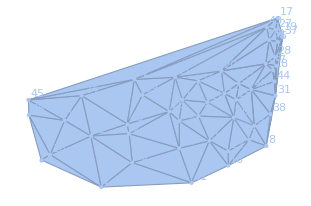

{4→2,2→26,26→4,2→42,42→26,35→4,26→35,24→10,10→42,42→24,10→26,5→48,48→42,42→5,48→24,2→29,29→42,10→35,29→41,41→34,34→29,2→41,41→3,3→34,34→5,5→29,34→25,25→5,14→34,3→14,3→23,23→14,25→48,41→16,16→3,14→25,45→35,10→45,25→39,39→48,24→45,48→32,32→24,39→32,21→32,39→21,32→45,25→21,32→17,17→45,13→23,23→11,11→13,13→25,14→13,40→11,23→40,11→47,47→13,21→47,47→20,20→21,21→13,12→20,47→12,21→43,43→32,11→12,20→43,3→40,40→22,22→1,1→40,3→22,9→15,15→40,40→9,40→12,12→15,15→33,33→12,46→33,15→46,20→33,33→36,36→20,22→16,16→1,1→8,8→9,9→1,16→8,8→38,38→9,9→46,46→38,38→31,31→46,8→31,46→36,44→46,31→44,46→18,18→36,44→18,7→36,18→7,28→36,7→28,27→43,43→30,30→27,20→30,28→30,30→36,6→30,28→6,44→7,37→6,28→37,31→7,37→19,19→6,6→27,27→19,19→17,17→27,17→43,7→37,31→37}

```mathematica
DelaunayMesh[Pin];
HighlightMesh[%,Labeled[0,"Index"]]
Ruleg=EdgeRulesMesh[%]
```

```mathematica
Ruleg={4->2,2->26,26->4,2->42,42->26,35->4,26->35,24->10,10->42,42->24,10->26,5->48,48->42,42->5,48->24,2->29,29->42,10->35,29->41,41->34,34->29,2->41,41->3,3->34,34->5,5->29,34->25,25->5,14->34,3->14,3->23,23->14,25->48,41->16,16->3,14->25,45->35,10->45,25->39,39->48,24->45,48->32,32->24,39->32,21->32,39->21,32->45,25->21,32->17,17->45,13->23,23->11,11->13,13->25,14->13,40->11,23->40,11->47,47->13,21->47,47->20,20->21,21->13,12->20,47->12,21->43,43->32,11->12,20->43,3->40,40->22,22->1,1->40,3->22,9->15,15->40,40->9,40->12,12->15,15->33,33->12,46->33,15->46,20->33,33->36,36->20,22->16,16->1,1->8,8->9,9->1,16->8,8->38,38->9,9->46,46->38,38->31,31->46,8->31,46->36,44->46,31->44,46->18,18->36,44->18,7->36,18->7,28->36,7->28,27->43,43->30,30->27,20->30,28->30,30->36,6->30,28->6,44->7,37->6,28->37,31->7,37->19,19->6,6->27,27->19,19->17,17->27,17->43,7->37,31->37};
```

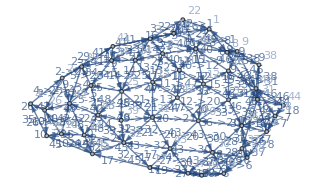

```mathematica
Gin=Graph[Ruleg,VertexLabels->"Name",EdgeLabels->"Name"](*Ggraph input*)
```

```mathematica
FundLoop=FindFundamentalCycles[UndirectedGraph[Gin]];
```

```mathematica
RuleFundLoop=Table[EdgeRules[FundLoop[[i]]],{i,Length[FundLoop]}];
```

```mathematica
RuleRevFundLoop=Table[EdgeRules[ReverseGraph[Graph[RuleFundLoop[[i]]]]],{i,Length[FundLoop]}];
```

```mathematica
h=Table[
Table[
If[MemberQ[RuleFundLoop[[j]],Ruleg[[i]]],1,0]+If[MemberQ[RuleRevFundLoop[[j]],Ruleg[[i]]],-1,0],
{i,EdgeCount[Gin]}
],
{j,Length[FundLoop]}] ;(* 検算済 *)
```

```mathematica
PD=PDDelaunay=Table[
EuclideanDistance[
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[1,1]]]],
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[2,1]]]]
],
{i,Length[EdgeRules[Gin]]}];(* Point Distance *)
r=IdentityMatrix[Length[EdgeRules[Gin]]]PD;
s=Table[0,{i,Length[EdgeRules[Gin]]}];
FLP=Table[
Pin[[
ConnectedComponents[RuleFundLoop[[i]]][[1]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Point *)
LoopSpin=Table[
If[(Append[FLP[[i,2]]-FLP[[i,1]],0]×Append[FLP[[i,3]]-FLP[[i,2]],0]).{0,0,1}>0,1,-1],
{i,Length[RuleFundLoop]}];(* 右回りならば負、左回りならば正 *)
FLA=Table[
Area[Polygon[
Pin[[ConnectedComponents[RuleFundLoop[[i]]][[1]]]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Area *)
U=Table[LoopSpin[[i]]FLA[[i]],{i,Length[RuleFundLoop]}];(* 誘導起電力は右回りなら負、左回りなら正 *)
```

```mathematica
Curr=Transpose[h].Inverse[h.r.Transpose[h]//N].(h.s+U)(* 誘導起電力行列を考慮した電流を求める式 *)
```

{865.652,-795.469,-17.0923,51.325,-363.977,882.745,-760.076,398.07,431.593,-267.613,382.278,-783.041,-337.004,691.105,3.09797,885.461,-86.3992,-7.27015,-18.2789,309.111,352.571,724.336,-155.054,1152.23,-2719.18,-1342.71,2845.29,-97.6799,-982.657,-2848.07,-325.154,4655.96,-128.533,551.999,-341.85,6247.63,1650.09,-408.531,108.871,204.586,264.621,-373.082,927.206,-178.33,91.5484,82.6159,694.88,635.321,-1018.53,1099.12,7942.63,2147.7,-8863.94,-8574.94,-3457.09,471.307,813.821,6513.71,6605.68,-2125.75,-54.6416,1188.35,5083.03,3092.32,-2163.08,-1142.54,1063.42,4969.23,-586.719,976.516,-929.088,-25.6492,1551.65,547.578,3272.19,-2035.35,-2764.19,4528.61,-6309.14,16612.6,-10551.6,-36897.6,-17614.2,5024.48,-4708.93,1350.16,-355.861,278.008,-366.864,-131.919,932.43,259.98,-748.155,1408.17,-5692.56,5449.03,3292.7,-8996.47,773.19,-23504.7,-10933.3,3255.08,11716.8,11343.9,6721.08,6257.56,7093.96,12203.5,10882.1,-361.929,-3345.86,-7157.61,-1238.28,-928.334,-241.147,-1886.29,74.685,7467.28,1811.24,-467.721,5513.21,4949.86,-907.489,2864.73,-4018.45,1838.9,-87.4952,-191.255,2934.75,4294.07}

```mathematica
hrth=h.r.Transpose[h]//N;
```

```mathematica
Curr=Transpose[h].Inverse[hrth,Method->"CofactorExpansion"].(h.s+U)(* 誘導起電力行列を考慮した電流を求める式 *)
```

General::munfl: -(2.80878×10^-302)/(7.3049×10^8)は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

Inverse::sing: 行列{{43.7353,21.,-7.2111,21.,0.,21.,0.,0.,0.,0.,-7.2111,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-7.2111,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«40»},«49»,«40»}は特異行列です．

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1},138,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}.1.{-42,-5911/2,86,53/2,-40}
 |  |  |  |

```mathematica
Curr=Transpose[h].Inverse[hrth,Method->"OneStepRowReduction"].(h.s+U)(* 誘導起電力行列を考慮した電流を求める式 *)
```

{-0.654196,-3.20093,4.09324,3.7544,-3.37937,-0.832636,2.2142,-5.07997,7.62543,-2.9511,5.62224,3.85149,-2.91763,11.4242,6.0351,4.41517,1.33071,-1.37526,1.9539,5.04144,2.47391,1.99951,-4.67137,-5.75939,12.3478,5.40614,-6.70909,-2.2581,18.5157,-7.37184,2.96783,-18.9157,-3.65678,17.461,-23.9011,13.3396,4.161,-29.7987,-21.9275,-9.9807,-2.99811,-10.103,3.50312,-1.92314,11.3055,35.7928,-6.12381,-1.49767,2.94439,5.99167,-3.18364,34.6687,-33.9573,-24.782,12.2418,-3.47947,1.48765,28.0031,2.12878,-30.2314,40.2314,30.8246,33.6613,55.273,-4.83234,-22.2704,-48.3573,-13.4684,-15.3893,17.3514,-9.24166,8.19486,8.27811,29.3309,8.64518,-0.753295,3.88209,-0.0961597,4.45748,14.9826,-0.278181,-18.606,12.4903,-3.26444,-3.92843,-5.26661,7.28937,-7.02771,36.112,2.18925,2.83566,73.9626,-1.52636,-2.36922,9.63092,5.60007,6.44292,-18.5169,-18.3896,-11.8037,17.0085,-17.5158,-12.1275,-30.4382,50.535,-30.5002,13.0778,56.0134,-20.5387,-13.1398,4.39229,57.3021,-57.7689,-102.121,-103.703,49.5427,21.9479,-34.5123,14.6289,20.9897,23.0154,-42.4926,-26.1258,24.7555,-138.399,33.3035,28.9102,11.3706,-36.9366,51.9055,-62.2269,127.29,141.21,-3.77373,-48.1862,39.5728,26.3734,22.1615,46.6694,113.842}

```mathematica
Curr=Transpose[h].Inverse[h.r.Transpose[h],Method->"CofactorExpansion"].(h.s+U)(* 誘導起電力行列を考慮した電流を求める式 *)
```

$Aborted

```mathematica
Curr=Transpose[h].Inverse[h.r.Transpose[h],Method->"OneStepRowReduction"].(h.s+U)(* 誘導起電力行列を考慮した電流を求める式 *)
```

$Aborted

```mathematica
Curr=Transpose[h].Inverse[h.r.Transpose[h],Method->"DivisionFreeRowReduction"].(h.s+U)(* 誘導起電力行列を考慮した電流を求める式 *)
```

$Aborted

```mathematica
Curr={-0.6541956247817775,-3.2009321703626075,4.093244024841091,3.7544015706282456,-3.379372562195755,-0.8326360166149218,2.2142035858035545,-5.079972609400146,7.625432709564839,-2.9510957372237208,5.622241775115208,3.8514900294894074,-2.917632071282137,11.424238162587827,6.0350962365785,4.415174367829156,1.3307100347011815,-1.3752568791836945,1.9538986948262616,5.041437820168307,2.4739085241128658,1.9995148018092577,-4.671367134243307,-5.759391457776095,12.347775669295487,5.406136900114691,-6.709093724540049,-2.2580971338474467,18.51574423924136,-7.3718350087740845,2.9678297620170504,-18.91574691249322,-3.6567777537173556,17.46102354178519,-23.901116751535,13.339551762006872,4.160995211269801,-29.798714642404672,-21.927483390850085,-9.980696762561907,-2.998114550124047,-10.102951150138013,3.503115917917779,-1.923142498149427,11.305499296548701,35.79278538924215,-6.123805194684168,-1.4976674811732422,2.9443921664656005,5.99166987952774,-3.183638327401434,34.66865017432943,-33.95732323790492,-24.782015030975742,12.24181339180067,-3.479466294520077,1.4876451844227134,28.003139843113686,2.1287839346002704,-30.23138595403575,40.23140114019061,30.824599404515933,33.66130885009502,55.27300290000284,-4.832342203072237,-22.270390042709614,-48.35733438004277,-13.46838946536908,-15.38931393262986,17.35136563747597,-9.241655828096123,8.194861775753623,8.278106643180625,29.330850859894294,8.645176141407056,-0.7532946754489231,3.882094258124488,-0.09615972854155545,4.45747557728968,14.982598058568314,-0.27818104191744975,-18.60600305823082,12.490290221459482,-3.264444785082888,-3.928425096468647,-5.26661470292475,7.289371664687792,-7.027709263915455,36.11197342104782,2.1892530796785037,2.8356644541923925,73.96259528230279,-1.5263582739392545,-2.369215789560757,9.630922564370202,5.6000651097633325,6.442922625384831,-18.516942662094962,-18.38958475867349,-11.803692212823345,17.00854417338797,-17.515829567533068,-12.127496257352433,-30.438247142171218,50.535023222241364,-30.50020551275876,13.077847337720709,56.013405076932806,-20.538680255643463,-13.139805708308238,4.39228637021905,57.302137435808184,-57.76892379496779,-102.12121672727702,-103.70333753017319,49.54265529322278,21.9479202056795,-34.51230676758107,14.628922201189557,20.989666551128387,23.015434089532945,-42.49257414801077,-26.12579487923769,24.755515608339664,-138.3988932983702,33.303525150996286,28.910227044905213,11.370563146398467,-36.93658449911504,51.905478324470465,-62.226866600266966,127.28997794071377,141.20969689546718,-3.7737326806682816,-48.18617318932101,39.57277758008429,26.37339415533205,22.16149797679109,46.66941430903637,113.84237843657522};
```

```mathematica
Gout=GDelaunay=Graph[Table[If[Curr[[i]]>0,
VertexList[{EdgeRules[Gin][[i]]}][[1]]->VertexList[{EdgeRules[Gin][[i]]}][[2]],
VertexList[{EdgeRules[Gin][[i]]}][[2]]->VertexList[{EdgeRules[Gin][[i]]}][[1]]
],{i,Length[EdgeRules[Gin]]}
]];(* 電流値の正負をグラフの向きに反映した出力グラフ *)
```

### TSPの解

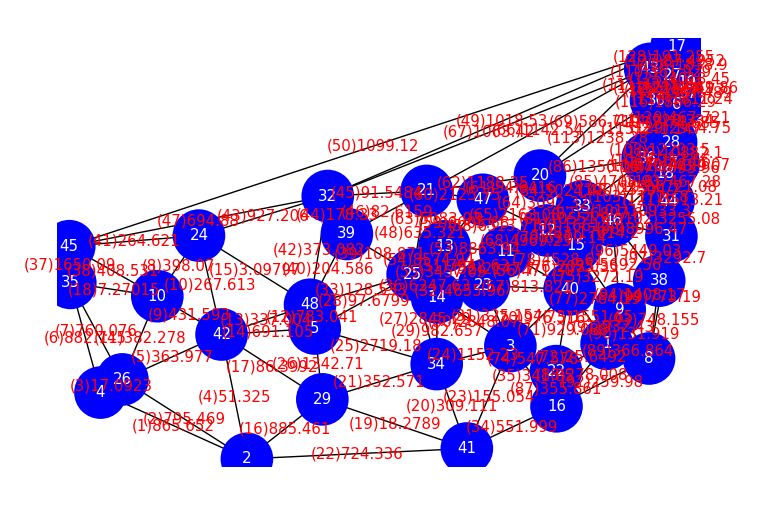

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gout][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gout][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gout]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[Style["("<>TextString[i]<>")"<>TextString[Abs[Curr[[i]]]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```

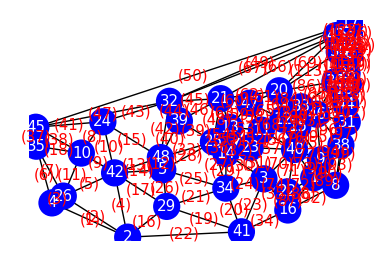

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gout][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gout][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gout]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[Style["("<>TextString[i]<>")",FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```

```mathematica
Grid[{EdgeRules[Gin][[1;;10]],Range[10]},Frame->All]
Grid[{EdgeRules[Gin][[11;;20]],Range[11,20]},Frame->All]
Grid[{EdgeRules[Gin][[21;;30]],Range[21,30]},Frame->All]
Grid[{EdgeRules[Gin][[31;;40]],Range[31,40]},Frame->All]
Grid[{EdgeRules[Gin][[41;;45]],Range[41,45]},Frame->All]
```

4→2 | 2→26 | 26→4 | 2→42 | 42→26 | 35→4 | 26→35 | 24→10 | 10→42 | 42→24
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10

10→26 | 5→48 | 48→42 | 42→5 | 48→24 | 2→29 | 29→42 | 10→35 | 29→41 | 41→34
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20

34→29 | 2→41 | 41→3 | 3→34 | 34→5 | 5→29 | 34→25 | 25→5 | 14→34 | 3→14
21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30

3→23 | 23→14 | 25→48 | 41→16 | 16→3 | 14→25 | 45→35 | 10→45 | 25→39 | 39→48
31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40

24→45 | 48→32 | 32→24 | 39→32 | 21→32
41 | 42 | 43 | 44 | 45

```mathematica
PDCurrCost=Abs[PD/Curr ]
```

{2.32387,2.32461,18.7128,30.9966,3.74402,1.61543,1.80835,2.31475,2.1696,4.7527,2.95818,0.387955,3.46629,1.69064,528.806,1.35882,17.3655,151.542,104.495,3.63352,4.24796,3.80358,8.99608,0.823879,0.584677,0.665123,0.408959,14.3337,0.851782,0.38719,2.54377,0.129968,10.4179,2.2472,2.7797,0.0670335,0.278884,3.10353,8.87867,4.88619,6.15386,3.70149,1.81899,2.98677,13.541,13.7456,4.74266,1.67111,4.6667,7.28226,0.0876915,0.233801,0.0863079,0.0620501,0.186827,1.97523,1.31851,0.109119,0.114343,0.334339,14.2118,1.2033,0.143595,0.224341,0.412109,2.79039,4.0797,0.117811,3.27609,1.05163,1.1183,28.0693,0.531249,1.19004,0.29636,0.271818,0.244195,0.174456,0.0642394,0.0298765,0.0502356,0.0114203,0.031492,0.130087,0.216872,1.01137,1.23936,3.61099,1.53273,5.44197,0.495568,5.01481,1.31554,0.433662,0.195295,0.174413,0.175428,0.0847629,2.0155,0.038344,0.0680358,0.135013,0.0756393,0.0251688,0.0526899,0.0529039,0.0236708,0.0291624,0.0245287,0.791316,0.119414,0.0521215,1.39907,0.60106,3.04545,0.138081,6.44952,0.0644511,0.1138,1.3952,0.166043,0.0265601,0.322402,0.127366,0.0501083,0.259185,4.22047,2.28381,0.30636,0.420831}

```mathematica
PDCurrCostSort=Ordering[PDCurrCost](* 昇順 *)
```

{82,107,109,104,122,108,80,83,100,125,81,112,105,106,54,79,118,36,101,103,98,53,51,58,119,59,68,111,124,32,84,102,116,63,121,96,78,97,55,95,85,64,52,77,126,76,37,75,129,123,60,30,12,27,65,130,94,91,73,25,114,26,110,24,29,86,70,71,74,62,87,93,57,16,120,113,89,6,48,14,7,43,56,99,9,34,128,8,1,2,31,35,66,11,44,115,38,69,13,88,20,42,5,22,67,127,21,49,47,10,40,92,90,41,117,50,39,23,33,45,46,61,28,17,3,72,4,19,18,15}

```mathematica
FindShortestTour[Pin,PerformanceGoal->"Speed"]
Graphics[Line[Pin[[Last[%]]]]]
```

{15 √2245+3 √3133+25 √3589+2 √4321+19 √4453+3 √4505+6 √5365+4 √13345+3 √17737+4 √19130+3 √19729+3 √21613+5 √27365+2 √41066+√42485+5 √61549+√71249+3 √90253+√92285+√102301+2 √106805+√125410+√136361+2 √146317+√175394+√190786+√211769+√232018+√283105+√283697+√316186+√333658+√342730+2 √361913+√366178+2 √384185+√424637+√455629+√539345+√603034+√849041+2 √854845+√968705+√999290+√1261493+√1365181+√1617689+√2033509,{1,9,40,15,12,11,13,25,14,23,3,22,16,41,34,29,2,26,4,35,45,10,24,42,5,48,39,32,21,47,20,33,46,36,30,43,17,27,19,37,6,28,7,18,44,31,38,8,1}}

-Graphics-

### 一貫した新しいgreedyを用いた解法4

```mathematica
GreedyDirectedPartLoop[PDCurrCostSort]
```

{33→46,46→15,15→33}

```mathematica
PartLoop1={33->46,46->15,15->33};
```

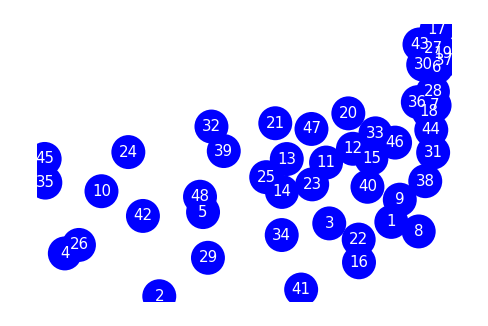

```mathematica
Graphics[{Table[Line[Pin[[VertexList[{i}]]]],{i,PartLoop1}],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
```

```mathematica
{20->3,3->22,22->2,2->20}
{2->16,16->29,29->20,20->2}
{2->29,29->20,20->2}
```

```mathematica
PartLoopProcess
```

{{2->29,29->20,20->2}}

```mathematica
OutEdgeRank[PartLoop1,PDCurrCostSort]
```

{61,140,92,115,114,116,135,108,64,105,112,104,113,137,67,131,129,136,106,60,52,74,89,122,118,62,46,38,58,29,53,127,98,39,101,109,63,130,121,102,110,119,107,82,54,126,35,70,34,36,138,99,66,69,83,120,139,25,117,68,128,40,100,103,14,123,32,26,95,80,71,50,30,124,24,73,72,45,75,88,11,87,27,111,42,86,65,23,2,20,77,55,15,8,47,84,134,96,9,5,13,97,85,43,3,56,16,31,41,12,51,33,91,28,4,49,44,94,10,22,19,59,7,93,90,21,37,76,79,18,17,1,48,6,57,81,78}

```mathematica
EdgeRules[Gout][[61]]
```

```mathematica
EdgeRules[Gout][[OutEdgeRank[PartLoop1,PDCurrCostSort]]]
```

{51→46,2→16,11→32,22→2,2→11,22→1,35→20,9→34,48→8,34→21,32→2,34→50,1→2,35→36,8→1,29→35,16→29,35→3,50→21,27→51,23→48,32→27,11→46,3→22,28→22,46→27,6→23,47→51,27→6,12→47,7→48,16→21,30→34,51→12,49→9,16→9,48→26,21→35,3→28,38→9,16→50,28→31,50→9,5→49,26→7,20→22,46→5,48→6,12→5,46→12,36→3,49→30,1→48,27→48,5→38,8→22,21→36,15→37,31→22,1→27,21→29,14→25,10→49,9→30,47→18,36→28,6→47,37→17,30→10,5→15,31→8,23→7,17→4,36→31,15→44,46→32,31→26,24→6,37→5,16→38,4→18,16→11,17→47,1→32,25→24,38→49,26→8,44→37,41→19,44→17,45→33,26→43,18→25,13→41,43→24,11→38,20→3,33→39,13→40,19→42,47→4,39→34,5→11,18→14,41→40,6→14,25→13,37→12,24→14,18→13,43→7,18→6,33→10,12→17,40→42,43→23,24→23,30→39,4→13,45→44,42→44,6→51,4→41,39→10,10→15,42→45,40→45,45→15,40→33,42→17,42→4,19→40,25→43,4→19,43→13,49→15,15→33}

```mathematica
OutEdgeRank1={51->46,2->16,11->32,22->2,2->11,22->1,35->20,9->34,48->8,34->21,32->2,34->50,1->2,35->36,8->1,29->35,16->29,35->3,50->21,27->51,23->48,32->27,11->46,3->22,28->22,46->27,6->23,47->51,27->6,12->47,7->48,16->21,30->34,51->12,49->9,16->9,48->26,21->35,3->28,38->9,16->50,28->31,50->9,5->49,26->7,20->22,46->5,48->6,12->5,46->12,36->3,49->30,1->48,27->48,5->38,8->22,21->36,15->37,31->22,1->27,21->29,14->25,10->49,9->30,47->18,36->28,6->47,37->17,30->10,5->15,31->8,23->7,17->4,36->31,15->44,46->32,31->26,24->6,37->5,16->38,4->18,16->11,17->47,1->32,25->24,38->49,26->8,44->37,41->19,44->17,45->33,26->43,18->25,13->41,43->24,11->38,20->3,33->39,13->40,19->42,47->4,39->34,5->11,18->14,41->40,6->14,25->13,37->12,24->14,18->13,43->7,18->6,33->10,12->17,40->42,43->23,24->23,30->39,4->13,45->44,42->44,6->51,4->41,39->10,10->15,42->45,40->45,45->15,40->33,42->17,42->4,19->40,25->43,4->19,43->13,49->15,15->33};
```

```mathematica
Gout=Gin=GOrigin; (* 閉路、枝、点をつなぎ合わせるときは、完全グラフを想定する必要がある *)
PD=PDOrigin;
```

```mathematica
InsertEdge[PartLoop1,51->46]
```

{29→20,20→2,51→46,2→51,29→46}

```mathematica
PartLoop2={29->20,20->2,51->46,2->51,29->46};
```

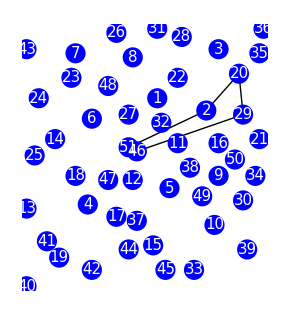

```mathematica
Graphics[{Line[Pin[[VertexSortFromLoopEdgeList[PartLoop2]]]],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
```

```mathematica
GreedyDirectedPartLoop[OutEdgeRank1]
```

{2→11,11→32,32→2}

```mathematica
PartLoop2=InsertVertex[PartLoop1,3]
```

{2→29,29→20,3→20,2→3}

```mathematica
InsertEdge[PartLoop1,2->16]
```

{29→20,20→2,2→16,16→29}

```mathematica
PartLoop2={29->20,20->2,2->16,16->29};
```

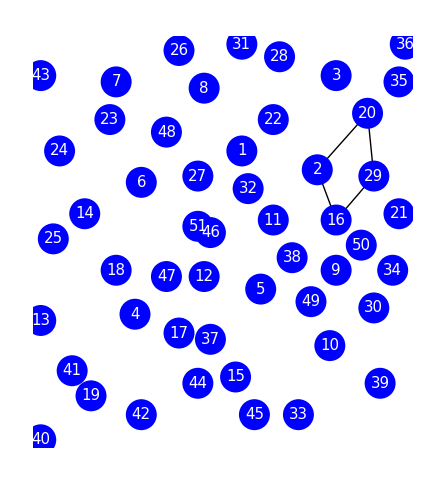

```mathematica
Graphics[{Line[Pin[[VertexSortFromLoopEdgeList[PartLoop2]]]],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
```

```mathematica
VertexSortFromLoopEdgeList[PartLoop2]
```

{2,20,29,16,2}

```mathematica
InsertEdge[PartLoop2,11->32]
```

{29→20,20→2,16→29,11→32,2→32,16→11}

```mathematica
PartLoop3={29->20,20->2,16->29,11->32,2->32,16->11};
```

```mathematica
VertexSortFromLoopEdgeList[PartLoop3]
```

{2,20,29,16,11,32,2}

```mathematica
InsertEdge[PartLoop3,22->2]
```

{29→20,20→2,16→29,11→32,16→11,22→2,22→32}

```mathematica
PartLoop4={29->20,20->2,16->29,11->32,16->11,22->2,22->32};
```

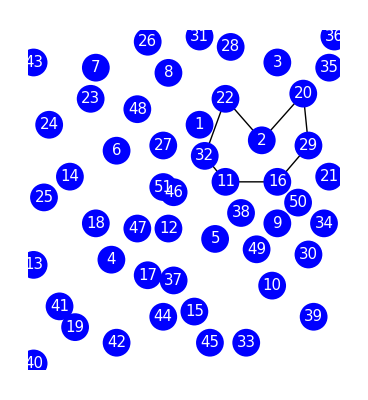

```mathematica
Graphics[{Line[Pin[[VertexSortFromLoopEdgeList[PartLoop4]]]],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
```

```mathematica
Gout=Gin=GDelaunay; (* 外側の点を挿入するときは再度ドロネー図を読み込む *)
PD=PDDelaunay;
```

#### 重み付け

```mathematica
PDWeight=PD*Table[1+i*0.1,{i,Length[PD]}][[Ordering[Ordering[PD]]]]
```

{126.499,5.5,154.663,94.0068,72.624,209.66,184.315,97.17,39.9,214.976,57.1183,73.5532,61.701,66.1105,44.7214,177.565,235.659,201.881,118.4,73.4784,36.,119.429,51.6888,38.3214,34.6133,29.5743,85.7418,104.398,7.2,57.8799,107.534,225.101,106.29,86.6637,149.316,19.0919,506.67,98.1134,66.9167,42.9009,64.622,196.499,120.459,99.0568,192.212,45.8394,66.7943,349.429,173.411,38.9297,150.52,87.5857,36.2039,46.9574,98.387,121.488,93.6,80.5929,139.101,11.2,7.82624,88.5076,178.88,89.4296,35.3344,68.0312,71.1376,67.723,75.7005,34.8827,90.3515,108.539,91.2735,42.8803,37.3352,24.1495,9.1,72.3038,617.92,107.746,57.6999,43.7049,19.799,24.8204,48.0755,58.6415,17.,92.1954,60.1684,74.3135,155.871,43.5412,18.,151.724,93.1174,193.605,166.619,25.4912,109.544,59.403,44.1816,52.4168,26.3044,44.8219,81.4985,62.482,14.1421,14.4,12.,14.7078,39.538,140.242,69.2682,127.562,128.625,20.5061,24.7,110.549,28.4605,157.08,43.6394,161.127,229.137,59.8,152.928,216.479,111.554,36.0555,94.0394,46.2,226.653,112.559,82.404,63.263,21.2132,113.564,40.1462,158.288,402.576,74.3328}

```mathematica
PDCurrCostSort
```

{61,133,140,132,92,125,115,114,116,135,108,64,105,112,104,113,137,67,131,129,136,106,60,52,74,89,122,118,62,46,38,58,29,53,127,98,39,101,109,63,130,121,102,110,119,107,82,54,126,35,70,34,36,138,99,66,69,83,120,139,25,117,68,128,40,100,103,14,123,32,26,95,80,71,50,30,124,24,73,72,45,75,88,11,87,27,111,42,86,65,23,2,20,77,55,15,8,47,84,134,96,9,5,13,97,85,43,3,56,16,31,41,12,51,33,91,28,4,49,44,94,10,22,19,59,7,93,90,21,37,76,79,18,17,1,48,6,57,81,78}

```mathematica
PDWeightCurrRank=Ordering[Abs[PDWeight/Curr]]
```

{61,108,60,29,116,135,133,109,92,140,132,130,53,107,125,110,117,113,115,114,46,98,36,74,67,104,137,83,105,64,89,2,54,121,119,70,106,103,87,77,82,124,112,52,129,101,25,136,62,58,102,39,66,128,118,38,131,122,127,40,75,69,34,68,100,9,63,26,14,99,35,50,126,24,138,80,65,15,120,84,30,55,139,123,111,95,71,11,47,73,23,86,93,32,85,27,88,72,21,20,134,45,12,8,42,13,5,41,4,97,33,76,90,43,96,56,31,3,16,28,51,44,91,49,22,19,57,94,59,10,7,37,79,18,17,1,81,48,6,78}

```mathematica
GreedyDirectedPartLoop[PDWeightCurrRank]
```

{20→2,2→29,29→20}

```mathematica
PartLoop1={20->2,2->29,29->20}
```

{20→2,2→29,29→20}

```mathematica
OutEdgeRank[PartLoop1,PDCurrCostSort]
```

{61,140,92,115,114,116,135,108,64,105,112,104,113,137,67,131,129,136,106,60,52,74,89,122,118,62,46,38,58,29,53,127,98,39,101,109,63,130,121,102,110,119,107,82,54,126,35,70,34,36,138,99,66,69,83,120,139,25,117,68,128,40,100,103,14,123,32,26,95,80,71,50,30,124,24,73,72,45,75,88,11,87,27,111,42,86,65,23,2,20,77,55,15,8,47,84,134,96,9,5,13,97,85,43,3,56,16,31,41,12,51,33,91,28,4,49,44,94,10,22,19,59,7,93,90,21,37,76,79,18,17,1,48,6,57,81,78}

```mathematica
EdgeRules[Gout][[{61,140,92,115,114,116,135,108,64,105,112,104,113,137,67,131,129,136,106,60,52,74,89,122,118,62,46,38,58,29,53,127,98,39,101,109,63,130,121,102,110,119,107,82,54,126,35,70,34,36,138,99,66,69,83,120,139,25,117,68,128,40,100,103,14,123,32,26,95,80,71,50,30,124,24,73,72,45,75,88,11,87,27,111,42,86,65,23,2,20,77,55,15,8,47,84,134,96,9,5,13,97,85,43,3,56,16,31,41,12,51,33,91,28,4,49,44,94,10,22,19,59,7,93,90,21,37,76,79,18,17,1,48,6,57,81,78}]]
```

{51→46,2→16,11→32,22→2,2→11,22→1,35→20,9→34,48→8,34→21,32→2,34→50,1→2,35→36,8→1,29→35,16→29,35→3,50→21,27→51,23→48,32→27,11→46,3→22,28→22,46→27,6→23,47→51,27→6,12→47,7→48,16→21,30→34,51→12,49→9,16→9,48→26,21→35,3→28,38→9,16→50,28→31,50→9,5→49,26→7,20→22,46→5,48→6,12→5,46→12,36→3,49→30,1→48,27→48,5→38,8→22,21→36,15→37,31→22,1→27,21→29,14→25,10→49,9→30,47→18,36→28,6→47,37→17,30→10,5→15,31→8,23→7,17→4,36→31,15→44,46→32,31→26,24→6,37→5,16→38,4→18,16→11,17→47,1→32,25→24,38→49,26→8,44→37,41→19,44→17,45→33,26→43,18→25,13→41,43→24,11→38,20→3,33→39,13→40,19→42,47→4,39→34,5→11,18→14,41→40,6→14,25→13,37→12,24→14,18→13,43→7,18→6,33→10,12→17,40→42,43→23,24→23,30→39,4→13,45→44,42→44,6→51,4→41,39→10,10→15,42→45,40→45,45→15,40→33,42→17,42→4,19→40,25→43,4→19,43→13,49→15,15→33}